# SpinDynamica Tutorial 01: Introduction to 2D NMR Simulation Using COSY

## Simulating, inspecting, processing, phasing, and visualizing homonuclear liquid-state 2D NMR spectra with Signal2D and Spectrum2D.

## 0. Setup and Loading SpinDynamica

Evaluate both setup cells in order. Cell 1 locates the SpinDynamica repository root upward from NotebookDirectory[] using System` symbols only and loads SpinDynamica`; Cell 2 verifies that the public 2D simulation and processing packages are available.

```mathematica
nbRepoRoot=Quiet[Check[NotebookDirectory[],Directory[]]];
While[StringQ[nbRepoRoot]&&nbRepoRoot=!=""&&!FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],With[{parent=ParentDirectory[nbRepoRoot]},If[parent===nbRepoRoot,nbRepoRoot=Directory[];Break[],nbRepoRoot=parent]]];
If[FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`",FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`"]];
```

SpinDynamica version SDv3.10.3b3 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

```mathematica
{MemberQ[$Packages,"Signals`Signal2D`"],MemberQ[$Packages,"Simulations`Signal2D`"],Context[Signal2D],Context[Spectrum2D]}
```

{True,True,Simulations`Signal2D`,Signals`Signal2D`}

## 1. Defining a Simple Two-Spin System

Every 2D NMR simulation in SpinDynamica begins with the spin system, its static Hamiltonian (the generator of free evolution), and an initial density operator. Here we define a weakly coupled homonuclear two-spin-1/2 AX system with two distinct, opposite-sign chemical shifts (-120 Hz and +180 Hz) and a scalar coupling J = 24 Hz so that F1 frequency discrimination, diagonal peaks, and anti-phase COSY cross peaks are immediately clear.

```mathematica
SetSpinSystem[{{1,1/2},{2,1/2}}];
nu1=-120.;
nu2=180.;
j12=24.;
Hcosy=2.*Pi*(nu1*opI[1,"z"]+nu2*opI[2,"z"]+j12*(opI[1,"z"].opI[2,"z"]));
rho0=opI["z"];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Notice that all frequencies in Hcosy are expressed in rad s^-1 (2 Pi times Hz), matching SpinDynamica's standard angular-frequency convention. Throughout this notebook we retain this same AX spin system and Hamiltonian so each section isolates only the new options being introduced.

## 2. Your First Signal2D Simulation (COSY)

A conventional 2D experiment has four sequential stages: (1) Preparation, (2) Indirect evolution during t1, (3) Mixing, and (4) Direct evolution and detection during t2. In Signal2D, these map directly onto the Preparation, Evolution1, Mixing, and Evolution2 (or shared BackgroundGenerator) options, while the two positional arguments specify the t1 and t2 timing grids.

### 2.1 Shortest Meaningful Call and First 2D Spectrum

We start with the shortest practical COSY call, relying on defaults wherever appropriate: QuadratureMethod -> "States", InitialDensityOperator -> opI["z"], Observable -> All, Chronology -> "LeftToRight", and BackgroundGenerator shared across all four stages. The compact timing shorthand {{{swRad, nPoints}}} specifies an 800 Hz spectral width in both dimensions (64 indirect t1 increments by 128 direct t2 points).

```mathematica
sigCosy=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->Pulse[{Pi/2,"x"}],BackgroundGenerator->Hcosy,LineBroadening->22.]
```

SignalData2D[64 x 128, Quadrature -> States, Method -> {<|Space→Hilbert,Method→DoubleDiagonalization,SignalCalculationMethod→DoubleDiagonalization,Chronology→LeftToRight,QuadratureOrder→1,QuadratureSpins→{1,2},NormalizationFactor→1.,InitialTimePoint→0.,Period→None,CarouselAverage→False,OversamplingFactor1→1,AutomaticQuadratureEncoding→True,ChannelDependentPreparation→False,ChannelDependentMixing→False,HeteronuclearDetected→False,ChannelNorms→<|Cos→11.6078,Sin→11.7678|>,PreparationPhaseShifts→<|Cos→{0.},Sin→{-1.5708}|>,ReceiverPhaseShifts→<|Cos→{0.},Sin→{0.}|>,DiagnosticWarnings→{}|>,DoubleDiagonalization}]

Let us immediately Fourier-transform sigCosy with FT and plot its real absorptive component using PlotSpectrum2D.

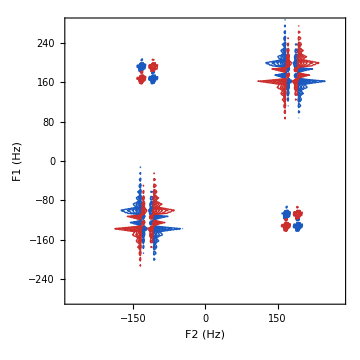

```mathematica
specCosy=FT[sigCosy,ZeroFill->{2,2}];
PlotSpectrum2D[specCosy,PlotRange->{{-280,280},{-280,280}},ImageSize->360]
```

What to observe: Two anti-phase 2x2 cross-peak multiplets appear at (F2 = +180 Hz, F1 = -120 Hz) and (F2 = -120 Hz, F1 = +180 Hz) in blue (positive) and red (negative), split by J = 24 Hz along both axes. The diagonal peaks sit at (-120 Hz, -120 Hz) and (+180 Hz, +180 Hz) with dispersive star-like tails, characteristic of a COSY-90 spectrum.

### 2.2 Making Important Options Explicit

In real workflows you will often customize individual stages. Below is the exact same COSY simulation with every major argument spelled out explicitly: initial state, background Hamiltonian, separate Evolution1/Evolution2 placeholders (None means use BackgroundGenerator directly), observable, NormalizationFactor, and explicit {tmin, tmax, dt} timing vectors. Two additional acquisition options worth knowing are Chronology ("LeftToRight" by default) and ForceEvenNumberOfPoints (False by default; set True to truncate odd increment counts cleanly for FFT).

```mathematica
dt=1./800.;
sigExplicit=Signal2D[{0.,63.*dt,dt},{0.,127.*dt,dt},InitialDensityOperator->rho0,BackgroundGenerator->Hcosy,Preparation->Pulse[{Pi/2,"x"}],Evolution1->None,Mixing->Pulse[{Pi/2,"x"}],Evolution2->None,Observable->All,NormalizationFactor->1,QuadratureMethod->"States",ForceEvenNumberOfPoints->False,LineBroadening->22.];
Max[Abs[sigExplicit["Cos"]-sigCosy["Cos"]]]
```

0.

The maximum numerical difference between the shorthand call and the explicit call is zero, confirming the defaults documented above.

## 3. Inspecting the Time-Domain SignalData2D Object

Signal2D returns a SignalData2D object that bundles the acquired quadrature channel matrices together with exact time axes and acquisition metadata. Using string property lookups avoids printing large numerical arrays.

```mathematica
{"Keys"->sigCosy["Keys"],"Dimensions"->sigCosy["Dimensions"],"QuadratureMethod"->sigCosy["QuadratureMethod"],"Timing1"->sigCosy["Timing1"],"Timing2"->sigCosy["Timing2"],"Channels"->Keys[sigCosy["Data"]],"Method"->sigCosy["Metadata"]["Method"],"Space"->sigCosy["Metadata"]["Space"]}//Dataset
```

Each channel matrix (here "Cos" and "Sin") has dimensions {N1, N2} = {64, 128}: row index k1 runs over the indirect t1 increments (sigCosy["Time1"]) and column index k2 runs over direct acquisition time t2 (sigCosy["Time2"]). Below we extract and plot a direct FID (row 5, t1 = 5 ms, since at t1 = 0 the two 90-degree x pulses cancel to zero) and an indirect interferogram trace (column 5, t2 = 5 ms, where J-evolution has built up strong observable coherence).

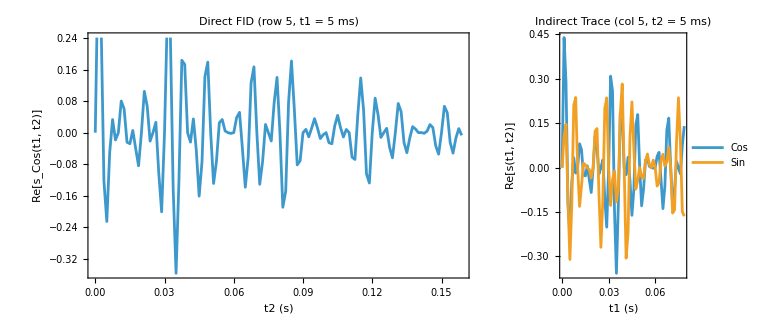

```mathematica
t1=sigCosy["Time1"];
t2=sigCosy["Time2"];
fidDirect=Re[sigCosy["Cos"][[5,All]]];
traceIndCos=Re[sigCosy["Cos"][[All,5]]];
traceIndSin=Re[sigCosy["Sin"][[All,5]]];
GraphicsRow[{ListLinePlot[Transpose[{t2,fidDirect}],Frame->True,FrameLabel->{"t2 (s)","Re[s_Cos(t1, t2)]"},PlotLabel->"Direct FID (row 5, t1 = 5 ms)"],ListLinePlot[{Transpose[{t1,traceIndCos}],Transpose[{t1,traceIndSin}]},Frame->True,FrameLabel->{"t1 (s)","Re[s(t1, t2)]"},PlotLegends->Placed[{"Cos","Sin"},{0.85,0.85}],PlotLabel->"Indirect Trace (col 5, t2 = 5 ms)"]},ImageSize->760,Spacings->20]
```

Along t2 you see the decaying, multi-frequency COSY beat pattern, while along t1 the Cos and Sin channels oscillate in quadrature (90 degrees out of phase) across the indirect evolution grid.

## 4. Quadrature Acquisition Methods

To distinguish positive and negative frequencies (+F1 vs -F1) and obtain pure absorption lineshapes in 2D NMR, indirect-dimension quadrature detection is required. Signal2D supports six QuadratureMethod modes:
  - "PhaseModulated": single complex P-type/N-type dataset without indirect phase separation; yields phase-twist lineshapes that cannot be phased to pure absorption and are normally plotted in magnitude mode.
  - "States": acquires separate "Cos" and "Sin" datasets shifted by -Pi/(2q) in preparation phase; yields mirror-free pure absorption spectra.
  - "StatesTPPI": acquires "Cos" and "Sin" with alternating 180-degree preparation and receiver phase, shifting F1 axial artifacts to the spectral edge.
  - "EchoAntiEcho": acquires "Echo" (p1 = -q) and "AntiEcho" (p1 = +q) coherence pathways and recombines them into a hypercomplex spectrum.
  - "TPPI": acquires a single real-modulated matrix with 2*N1 increments at half the dwell time (dt1/2); real-only F1 Fourier transformation leaves an intrinsic conjugate mirror unless positive/negative halves are separated.
  - "OversampledStates": acquires both "Cos" and "Sin" at 2*N1 increments (dt1/2), supporting full mirror-free quadrature over doubled F1 bandwidth or projection onto TPPI.

We run the same COSY experiment across all six methods, process them identically with FT, and compare channel keys, dimensions, and normalized 2D spectra over the same axis window.

```mathematica
qMethods={"PhaseModulated","States","StatesTPPI","EchoAntiEcho","TPPI","OversampledStates"};
sigsQ=AssociationMap[Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->Pulse[{Pi/2,"x"}],BackgroundGenerator->Hcosy,QuadratureMethod->#,LineBroadening->22.]&,qMethods];
specsQ=AssociationMap[FT[sigsQ[#],ZeroFill->{2,2}]&,qMethods];
TableForm[Table[{qm,If[AssociationQ[sigsQ[qm]["Data"]],Keys[sigsQ[qm]["Data"]],"Matrix"],sigsQ[qm]["N1"],If[MatrixQ[sigsQ[qm]["Data"]],Length[sigsQ[qm]["Data"]],Length[sigsQ[qm]["Data"][[1]]]],specsQ[qm]["Representation"],NumberForm[Max[Abs[specsQ[qm]["RR"]]],4]},{qm,qMethods}],TableHeadings->{None,{"QuadratureMethod","Data Keys","Logical N1","Rows Stored","Representation","Max |RR|"}}]
```

QuadratureMethod | Data Keys | Logical N1 | Rows Stored | Representation | Max |RR|
PhaseModulated | Matrix | 64 | 64 | Complex | 0.02079
States | Cos
Sin | 64 | 64 | Hypercomplex | 0.03769
StatesTPPI | Cos
Sin | 64 | 64 | Hypercomplex | 0.03769
EchoAntiEcho | Echo
AntiEcho | 64 | 64 | Hypercomplex | 0.03769
TPPI | Matrix | 64 | 128 | TPPIHypercomplex | 0.03769
OversampledStates | Cos
Sin | 64 | 128 | Hypercomplex | 0.03777

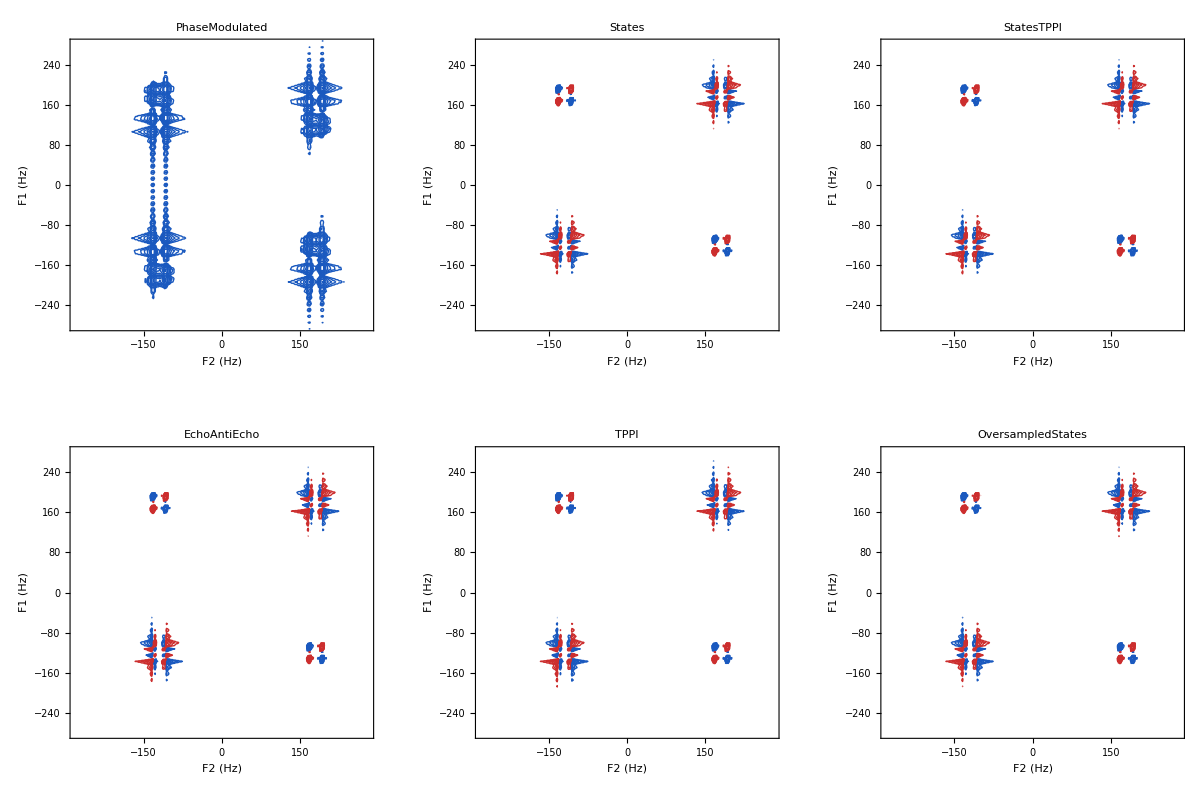

```mathematica
GraphicsGrid[Partition[Table[PlotSpectrum2D[specsQ[qm],PlotRange->{{-280,280},{-280,280}},Contours->8,BaseContourLevel->0.08,PlotLabel->qm,ImageSize->240],{qm,qMethods}],3],Spacings->10]
```

What to observe: "PhaseModulated" defaults to plotting "Magnitude" (positive contours only) because its real part has phase-twist lineshapes, whereas all five phase-sensitive methods display crisp signed absorption cross peaks. "States", "StatesTPPI", "EchoAntiEcho", "TPPI" (in default "RetainedHalf" mode), and "OversampledStates" (in default "Logical" bandwidth mode) agree closely here; differences between "PhaseModulated" and the others reflect phase-twist acquisition, while differences in TPPI come from its real-only F1 projection as explored further in Section 9.

## 5. Fourier Transformation and Processing (FT)

It is important to distinguish acquisition parameters (N1, N2, spectral widths, QuadratureMethod, pulse sequences) from processing parameters (zero-filling, apodization, first-point scaling, phase correction). By generating one unbroadened time-domain signal once, you can rapidly explore many processing choices without repeating the spin-dynamics calculation.

Pair-valued processing options in SpinDynamica follow {direct, indirect} = {F2, F1} ordering, matching Signals`Signal`.

```mathematica
sigRaw=Signal2D[{{{2Pi800.,64}},{{2Pi800.,128}}},Preparation->Pulse[{Pi/2,"x"}],Mixing->Pulse[{Pi/2,"x"}],BackgroundGenerator->Hcosy,QuadratureMethod->"States"];
```

### 5.1 Zero-Filling in F2 and F1

ZeroFill -> {zf2, zf1} pads the direct and indirect time axes before FFT, interpolating the frequency grid without adding simulation cost.

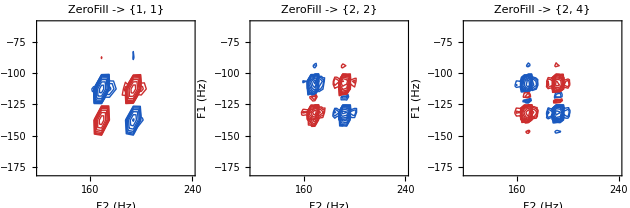

```mathematica
spZF11=FT[sigRaw,LineBroadening->22.,ZeroFill->{1,1}];
spZF22=FT[sigRaw,LineBroadening->22.,ZeroFill->{2,2}];
spZF24=FT[sigRaw,LineBroadening->22.,ZeroFill->{2,4}];
GraphicsRow[{PlotSpectrum2D[spZF11,PlotRange->{{120,240},{-180,-60}},PlotLabel->"ZeroFill -> {1, 1}",ImageSize->240],PlotSpectrum2D[spZF22,PlotRange->{{120,240},{-180,-60}},PlotLabel->"ZeroFill -> {2, 2}",ImageSize->240],PlotSpectrum2D[spZF24,PlotRange->{{120,240},{-180,-60}},PlotLabel->"ZeroFill -> {2, 4}",ImageSize->240]},Spacings->10]
```

### 5.2 Apodization and Time-Domain Line Broadening

Apodization shapes the FID before FFT to balance resolution and truncation artifacts. Supported windows include numeric exponential Lorentzian broadening, {"Lorentzian", lb}, {"Gaussian", fwhh}, {"Gaussian", lb, gb}, "SineBell", {"SineBell", shift}, "SquaredSineBell", and {"SquaredSineBell", shift}. You can pass Apodization or LineBroadening directly to FT, or pre-apply them to SignalData2D using ApplyApodization and ApplyLineBroadening.

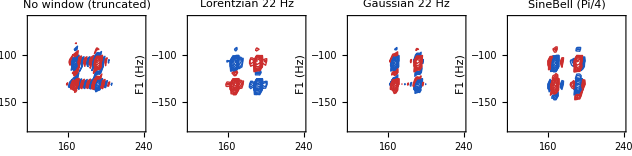

```mathematica
sigSinApo=ApplyApodization[sigRaw,Apodization->{{"SineBell",Pi/4},{"SineBell",Pi/4}}];
spNone=FT[sigRaw,ZeroFill->{2,2}];
spLorentz=FT[sigRaw,ZeroFill->{2,2},LineBroadening->{22.,22.}];
spGauss=FT[sigRaw,ZeroFill->{2,2},Apodization->{{"Gaussian",22.},{"Gaussian",22.}}];
spSine=FT[sigSinApo,ZeroFill->{2,2}];
GraphicsRow[{PlotSpectrum2D[spNone,PlotRange->{{120,240},{-180,-60}},PlotLabel->"No window (truncated)",ImageSize->220],PlotSpectrum2D[spLorentz,PlotRange->{{120,240},{-180,-60}},PlotLabel->"Lorentzian 22 Hz",ImageSize->220],PlotSpectrum2D[spGauss,PlotRange->{{120,240},{-180,-60}},PlotLabel->"Gaussian 22 Hz",ImageSize->220],PlotSpectrum2D[spSine,PlotRange->{{120,240},{-180,-60}},PlotLabel->"SineBell (Pi/4)",ImageSize->220]},Spacings->8]
```

### 5.3 First-Point Multiplication and Phase Correction

FirstPointMultiplicationFactor -> {f2, f1} (default 0.5 on both axes from Options[FT]) scales the t = 0 point to suppress constant DC baseline offsets arising from causal discrete integration. Setting {1.0, 1.0} disables this halving and leaves a tiny constant offset. PhaseCorrection accepts phi0, {phi0Dir, phi0Ind}, or {{phi0Dir, phi1Dir}, {phi0Ind, phi1Ind}} in radians (again {F2, F1} ordering).

```mathematica
spFpmf10=FT[sigRaw,LineBroadening->22.,ZeroFill->{2,2},FirstPointMultiplicationFactor->{1.0,1.0}];
spFpmf05=FT[sigRaw,LineBroadening->22.,ZeroFill->{2,2},FirstPointMultiplicationFactor->{0.5,0.5}];
spPhaseErr=FT[sigRaw,LineBroadening->22.,ZeroFill->{2,2},PhaseCorrection->{{0.55,-0.30},{-0.45,0.25}}];
{"Baseline Offset (FPMF 1.0 vs 0.5)"->{Mean[Flatten[spFpmf10["RR"]]],Mean[Flatten[spFpmf05["RR"]]]},"F1 Axis Range (Hz)"->MinMax[spFpmf05["Frequency1"]],"F2 Axis Range (rad/s)"->MinMax[spFpmf05["AngularFrequency2"]]}
```

{Baseline Offset (FPMF 1.0 vs 0.5)→{-7.04096×10^-21,-8.04681×10^-21},F1 Axis Range (Hz)→{-393.75,400.},F2 Axis Range (rad/s)→{-2493.64,2513.27}}

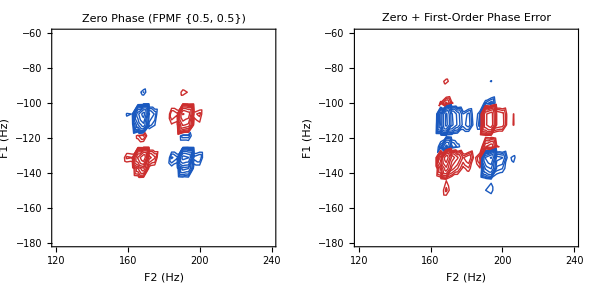

```mathematica
GraphicsRow[{PlotSpectrum2D[spFpmf05,PlotRange->{{120,240},{-180,-60}},PlotLabel->"Zero Phase (FPMF {0.5, 0.5})",ImageSize->280],PlotSpectrum2D[spPhaseErr,PlotRange->{{120,240},{-180,-60}},PlotLabel->"Zero + First-Order Phase Error",ImageSize->280]},Spacings->15]
```

Notice that spFpmf05["Frequency1"] and spFpmf05["Frequency2"] return frequency axes in Hz spanning (-SW/2, +SW/2], while "AngularFrequency1" and "AngularFrequency2" return 2 Pi times those frequencies in rad s^-1.

## 6. Hypercomplex Spectrum2D Objects

A phase-sensitive 2D FT spectrum has two independent imaginary units, i1 (for F1) and i2 (for F2), forming a bicomplex matrix S = U + i2 V with U = S_RR + i1 S_IR and V = S_RI + i1 S_II. Consequently, Spectrum2D stores four real components:
  - "RR" (Re/Re): pure absorption along both F1 and F2 when properly phased,
  - "IR" (Im/Re): dispersive in F1, absorptive in F2,
  - "RI" (Re/Im): absorptive in F1, dispersive in F2,
  - "II" (Im/Im): dispersive in both dimensions.
Because U and V carry independent phase planes, F1 and F2 phase corrections commute cleanly and can be applied independently after FT using PhaseSpectrum2D.

```mathematica
comps=specCosy["Components"];
{"Representation"->specCosy["Representation"],"HypercomplexQ"->specCosy["HypercomplexQ"],"ComponentKeys"->Keys[comps],"Max HypercomplexMagnitude"->Max[specCosy["HypercomplexMagnitude"]]}
```

{Representation→Hypercomplex,HypercomplexQ→True,ComponentKeys→{RR,IR,RI,II},Max HypercomplexMagnitude→0.0415793}

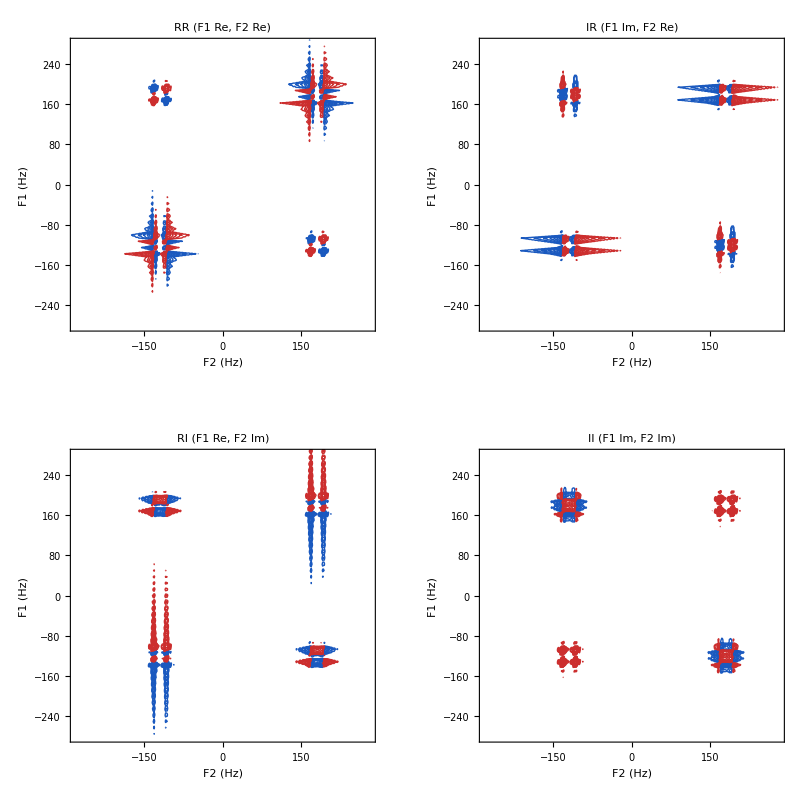

```mathematica
GraphicsGrid[{{PlotSpectrum2D[specCosy,Component->"RR",PlotRange->{{-280,280},{-280,280}},PlotLabel->"RR (F1 Re, F2 Re)",ImageSize->260],PlotSpectrum2D[specCosy,Component->"IR",PlotRange->{{-280,280},{-280,280}},PlotLabel->"IR (F1 Im, F2 Re)",ImageSize->260]},{PlotSpectrum2D[specCosy,Component->"RI",PlotRange->{{-280,280},{-280,280}},PlotLabel->"RI (F1 Re, F2 Im)",ImageSize->260],PlotSpectrum2D[specCosy,Component->"II",PlotRange->{{-280,280},{-280,280}},PlotLabel->"II (F1 Im, F2 Im)",ImageSize->260]}},Spacings->12]
```

You can also inspect the phase-independent "HypercomplexMagnitude" Sqrt[Abs[U]^2 + Abs[V]^2], and apply PhaseSpectrum2D to correct an arbitrary F2 + F1 zero- and first-order phase error back to the exact unperturbed spectrum.

```mathematica
specFixed=PhaseSpectrum2D[spPhaseErr,{{-0.55,0.30},{0.45,-0.25}}];
{"Max |RR_fixed - RR_ref|"->Max[Abs[specFixed["RR"]-spZF22["RR"]]]}
```

{Max |RR_fixed - RR_ref|→6.93889×10^-18}

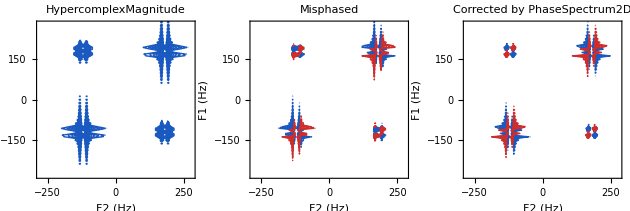

```mathematica
GraphicsRow[{PlotSpectrum2D[specCosy,Component->"HypercomplexMagnitude",PlotRange->{{-280,280},{-280,280}},PlotLabel->"HypercomplexMagnitude",ImageSize->260],PlotSpectrum2D[spPhaseErr,PlotRange->{{-280,280},{-280,280}},PlotLabel->"Misphased",ImageSize->260],PlotSpectrum2D[specFixed,PlotRange->{{-280,280},{-280,280}},PlotLabel->"Corrected by PhaseSpectrum2D",ImageSize->260]},Spacings->10]
```

## 7. Spectrum Manipulation and Plotting

It is helpful to separate display-only operations (which change only how PlotSpectrum2D renders the figure) from data-modifying operations (which return a new Spectrum2D with altered spectral arrays).

### 7.1 Display-Only Plotting, Slices, and Projections

PlotSpectrum2D supports styling and viewing options such as Component, Contours, BaseContourLevel, ContourFactor, PositiveColor, NegativeColor, PlotRange, ReverseAxes -> {revF2, revF1} (standard NMR convention is high-to-low ppm/Hz), AxisUnits -> "Hz" | "rad/s", and ShowProjections -> True (note: ShowProjections aligns the top/side skyline projections to the full frequency span, so use PlotRange -> All when enabling ShowProjections). ExtractSlice and ProjectSpectrum2D pull 1D cross-sections and projections directly from Spectrum2D.

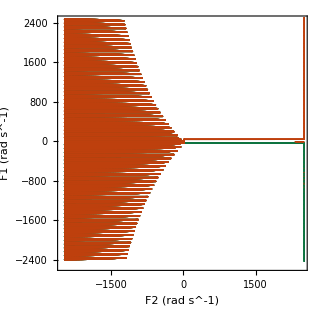
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
PlotSpectrum2D[spZF11,ReverseAxes->{True,True},AxisUnits->"rad/s",Contours->6,BaseContourLevel->0.08,ContourFactor->1.35,PositiveColor->RGBColor[0.05,0.45,0.25],NegativeColor->RGBColor[0.75,0.25,0.05],ShowProjections->True,PlotRange->All]
```

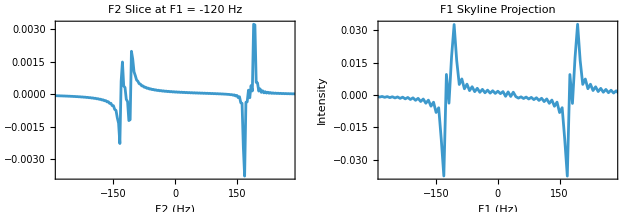

```mathematica
sliceF2=ExtractSlice[specCosy,"F2",-120.,PositionType->"Frequency"];
projF1=ProjectSpectrum2D[specCosy,"F1",Method->"Skyline"];
GraphicsRow[{ListLinePlot[sliceF2,Frame->True,PlotRange->{{-280,280},All},FrameLabel->{"F2 (Hz)","Intensity"},PlotLabel->"F2 Slice at F1 = -120 Hz",ImageSize->340],ListLinePlot[projF1,Frame->True,PlotRange->{{-280,280},All},FrameLabel->{"F1 (Hz)","Intensity"},PlotLabel->"F1 Skyline Projection",ImageSize->340]},Spacings->15]
```

### 7.2 Data-Modifying Operations: Reflection, Conjugation, and Combination

ReflectSpectrum[spec, Axis -> "F1" | "F2"] reverses the spectral grid along F1 or F2, ConjugateSpectrum2D[spec, "F1" | "F2"] conjugates along i1 (U -> U*, V -> V*) or i2 (V -> -V), and spectra can be scaled by numbers or combined via CombineData (for complementary P/N-type spectra acquired separately, CombineComplementarySpectra automates reflection and recombination).

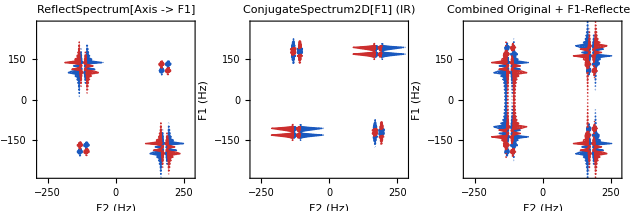

```mathematica
specRefF1=ReflectSpectrum[specCosy,Axis->"F1"];
specConjF1=ConjugateSpectrum2D[specCosy,"F1"];
specConjF2=ConjugateSpectrum2D[specCosy,"F2"];
specSym=CombineData[{0.5*specCosy,0.5*specRefF1}];
GraphicsRow[{PlotSpectrum2D[specRefF1,PlotRange->{{-280,280},{-280,280}},PlotLabel->"ReflectSpectrum[Axis -> F1]",ImageSize->240],PlotSpectrum2D[specConjF1,Component->"IR",PlotRange->{{-280,280},{-280,280}},PlotLabel->"ConjugateSpectrum2D[F1] (IR)",ImageSize->240],PlotSpectrum2D[specSym,PlotRange->{{-280,280},{-280,280}},PlotLabel->"Combined Original + F1-Reflected",ImageSize->240]},Spacings->10]
```

## 8. Full vs Compact Spectral Storage (StorageMode)

By default, FT uses StorageMode -> "Hypercomplex" (or Automatic), retaining both U and V so all four components (RR, IR, RI, II) remain accessible and F2 phase correction can still be adjusted interactively. Passing StorageMode -> "Compact" drops V immediately after the F2 Fourier transform (keeping only U = S_RR + i1 S_IR in Representation -> "ReducedComplex").

```mathematica
specFull=FT[sigCosy,ZeroFill->{2,2},StorageMode->"Hypercomplex"];
specCompact=FT[sigCosy,ZeroFill->{2,2},StorageMode->"Compact"];
{"Full Representation & Components"->{specFull["Representation"],Keys[specFull["Components"]]},"Compact Representation & Components"->{specCompact["Representation"],Keys[specCompact["Components"]]},"Compact HasDirectImaginary"->specCompact["QuadratureCapabilities"]["HasDirectImaginary"],"Compact F2 Phase Capability"->specCompact["QuadratureCapabilities"]["SupportsIndependentF2Phase"]}
```

{Full Representation & Components→{Hypercomplex,{RR,IR,RI,II}},Compact Representation & Components→{ReducedComplex,{RR,IR}},Compact HasDirectImaginary→False,Compact F2 Phase Capability→False}

In "Compact" storage, F1 phase adjustment still succeeds because U retains the F1 imaginary part S_IR, whereas attempting post-FT F2 phasing or F2 conjugation emits an informative diagnostic message (Spectrum2D::nof2phase / Spectrum2D::nocomp) and returns $Failed. Therefore, select StorageMode -> "Compact" only after finalizing any direct-dimension phase correction inside FT.

```mathematica
specCompactF1OK=PhaseSpectrum2D[specCompact,{{0.,0.},{0.4,0.}}];
{"F1 phase in Compact succeeded?"->(Head[specCompactF1OK]===Spectrum2D),"F2 phase in Compact (expected $Failed + nof2phase)"->PhaseSpectrum2D[specCompact,{{0.4,0.},{0.,0.}}],"F2 conjugation in Compact (expected $Failed + nocomp)"->ConjugateSpectrum2D[specCompact,"F2"]}
```

Spectrum2D::nof2phase: Cannot apply direct-dimension (F2) phase correction to a Spectrum2D with Representation -> ReducedComplex because direct-dimension imaginary components (RI, II) are not stored. Use default hypercomplex storage or apply F2 phasing inside FT.

Spectrum2D::nocomp: Component V is unavailable for Spectrum2D with Representation -> ReducedComplex.

{F1 phase in Compact succeeded?→True,F2 phase in Compact (expected $Failed + nof2phase)→$Failed,F2 conjugation in Compact (expected $Failed + nocomp)→$Failed}

## 9. OversampledStates and TPPI

Notice the close connection between OversampledStates and native TPPI:
  - "OversampledStates" acquires both "Cos" and "Sin" channels at 2*N1 increments with half the dwell time (dt1/2), giving a doubled F1 spectral width of 2*SW1.
  - Processing with IndirectBandwidth -> "Logical" (default) crops the central (-SW1/2, +SW1/2] window matching standard N1-point spectra, whereas IndirectBandwidth -> "Full" retains the entire 2*N1 mirror-free bandwidth.
  - Applying ProjectToTPPI[sigOS] computes the algebraic projection P_n = C_n Cos[n Pi/2] - S_n Sin[n Pi/2], turning an OversampledStates dataset into a real-modulated TPPI SignalData2D dataset without re-running the spin-dynamics simulation!

```mathematica
sigOS=sigsQ["OversampledStates"];
sigTPPI=sigsQ["TPPI"];
specOSLog=FT[sigOS,ZeroFill->{2,2},IndirectBandwidth->"Logical"];
specOSFull=FT[sigOS,ZeroFill->{2,2},IndirectBandwidth->"Full"];
sigProjTPPI=ProjectToTPPI[sigOS];
specProjTPPI=FT[sigProjTPPI,ZeroFill->{2,2},TPPIProcessing->"RetainedHalf"];
{"OS Logical N1 & SW1 (Hz)"->{specOSLog["N1"],specOSLog["SpectralWidth1Hz"]},"OS Full N1 & SW1 (Hz)"->{specOSFull["N1"],specOSFull["SpectralWidth1Hz"]},"PreservesFullHypercomplex? (Logical vs Full)"->{specOSLog["QuadratureCapabilities"]["PreservesFullHypercomplexSpectrum"],specOSFull["QuadratureCapabilities"]["PreservesFullHypercomplexSpectrum"]},"Max |ProjectToTPPI - native TPPI| (time domain)"->Max[Abs[sigProjTPPI["Data"]-sigTPPI["Data"]]],"Max |ProjectToTPPI - native TPPI| (RR spectrum)"->Max[Abs[specProjTPPI["RR"]-specsQ["TPPI"]["RR"]]]}
```

{OS Logical N1 & SW1 (Hz)→{128,800.},OS Full N1 & SW1 (Hz)→{256,1600.},PreservesFullHypercomplex? (Logical vs Full)→{False,True},Max |ProjectToTPPI - native TPPI| (time domain)→8.66126×10^-15,Max |ProjectToTPPI - native TPPI| (RR spectrum)→1.2837×10^-16}

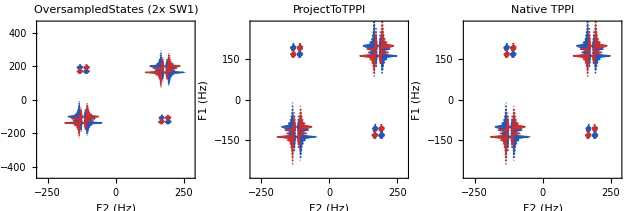

```mathematica
GraphicsRow[{PlotSpectrum2D[specOSFull,PlotRange->{{-280,280},{-450,450}},PlotLabel->"OversampledStates (2x SW1)",ImageSize->240],PlotSpectrum2D[specProjTPPI,PlotRange->{{-280,280},{-280,280}},PlotLabel->"ProjectToTPPI",ImageSize->240],PlotSpectrum2D[specsQ["TPPI"],PlotRange->{{-280,280},{-280,280}},PlotLabel->"Native TPPI",ImageSize->240]},Spacings->10]
```

Why is this useful? Native "TPPI" discards the orthogonal quadrature partner at each t1 point via time-proportional phase increments, so its real F1 transform inherently superimposes a small conjugate-mirror wing under finite damping or truncation (even when TPPIProcessing -> "RetainedHalf", "RealOnly", "Staggered", or "Hilbert" extracts the primary half-band). "OversampledStates" retains both channels, making it ideal whenever you want to explore full-bandwidth mirror-free F1 spectra or compare multiple processing/TPPI representations from one simulation.

## 10. Summary and Quick Reference

In a typical 2D simulation workflow:
  1. Define the spin system, static Hamiltonian, and pulse sequence stages using Signal2D (default QuadratureMethod -> "States" gives pure phase-sensitive absorption).
  2. Inspect SignalData2D channels, time axes, and metadata before processing.
  3. Apply FT with ZeroFill, Apodization or LineBroadening, FirstPointMultiplicationFactor, and PhaseCorrection in {F2, F1} order â.80.94 iterating freely without re-running Signal2D.
  4. Inspect hypercomplex components ("RR", "IR", "RI", "II") or phase errors with PhaseSpectrum2D, optionally switching to StorageMode -> "Compact" once F2 phasing is final, or using "OversampledStates" + ProjectToTPPI to compare acquisition schemes from one run.

Symbol / Option | Role | Typical Values & Ordering
Signal2D[t1, t2, opts] | Simulate 2D NMR time-domain data | Returns SignalData2D; timing {{swRad, n}} or {tmin, tmax, dt}
BackgroundGenerator | Static/stage evolution Hamiltonian | Operator, superoperator, or 4-stage list {bgPrep, bg1, bgMix, bg2}
Preparation / Mixing | Pulse sequences before/after t1 | Pulse[...], Delay[...], or list of events
QuadratureMethod | Indirect quadrature acquisition scheme | "States" (default), "StatesTPPI", "EchoAntiEcho", "TPPI", "OversampledStates", "PhaseModulated"
SignalData2D[...] | Inspect time-domain signals & metadata | "Cos", "Sin", "Echo", "AntiEcho", "Time1", "Time2", "Metadata"
FT[sig, opts] | 2D Fourier transform & processing | Pairs use {direct, indirect} = {F2, F1} ordering
ZeroFill / Apodization | Padding & windowing before FFT | ZeroFill -> {zf2, zf1}; Apodization / ApplyApodization / ApplyLineBroadening
FirstPointMultiplicationFactor | t = 0 point scaling for baseline | Scalar or {f2, f1} (e.g. {0.5, 0.5})
PhaseCorrection / PhaseSpectrum2D | Zero- and first-order phasing | {{ph0F2, ph1F2}, {ph0F1, ph1F1}} in radians
StorageMode | Post-F2 spectral storage representation | "Hypercomplex" (default U + i2 V) or "Compact" (U only)
IndirectBandwidth / TPPIProcessing | Special F1 FT controls | "Logical" / "Full" (OversampledStates); "RetainedHalf", "RealOnly", "Staggered", "Hilbert"
ProjectToTPPI[sigOS] | Project OversampledStates to TPPI | Computes P_n = C_n Cos[n Pi/2] - S_n Sin[n Pi/2]
Spectrum2D[...] | Inspect hypercomplex spectral data | "RR", "IR", "RI", "II", "HypercomplexMagnitude", "Frequency1", "Frequency2"
PlotSpectrum2D / ExtractSlice / ProjectSpectrum2D | Visualize & extract 1D slices/projections | Display-only: Component, ReverseAxes, PlotRange, ShowProjections
ReflectSpectrum / ConjugateSpectrum2D / CombineData | Modify or combine spectra | Axis -> "F1" | "F2"; linear combinations of compatible spectra